```mathematica
SetDirectory[NotebookDirectory[]];
log=False;
If[log==True,lp="ListLogLogPlot";p="LogLogPlot";,lp="ListPlot";p="Plot";]
```

```mathematica
data=Import["elap.out"];
xdata=Transpose[data][[1]];
ydata=Transpose[data][[2]]*xdata;
ListLogLogPlot[Transpose[{xdata,ydata}],Frame->{{True,False},{True,False}},FrameLabel->{"# cores","seconds"},FrameStyle->15,PlotRange->All]
```

{420.864,421.056,422.4,424.512,430.848}

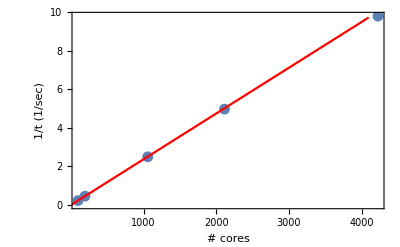

```mathematica
data=Import["prop.out"];
xdata=Transpose[data][[1]];
xdata*Transpose[data][[2]]
ydata=1/Transpose[data][[2]];
plotdata=Transpose[{xdata,ydata}];
p1=ToExpression[lp][plotdata,Frame->{{True,False},{True,False}},FrameLabel->{"# cores","1/t (1/sec)"},FrameStyle->15,PlotRange->All];
slope=plotdata[[1]][[2]]/plotdata[[1]][[1]];
p2=ToExpression[p][slope*x,{x,0.0001,4096},PlotStyle->Red];
Show[p1,p2]
```

```mathematica
slope
```

0.00237606